### Categorization

Tutorial

VQM

VQM`

VQM/tutorial/QuantumKernel1D

### Keywords

Details

# QuantumKernel1D

QSchroedinger1D | Solves the one-dimensional Schrödinger equation

C++ based solution of the one-dimensional  Schrödinger equation.

We load the package VQM, assuming that all files are properly installed.

```mathematica
Needs["VQM`"]
```

## Prepare the data

We are going to calculate the motion of a one-dimensional wave packet. The wave packet is a solution of the one-dimensional Schrödinger equation

ⅈ∂/(∂t)ψ(x,t) = -1/2∂^2/(∂x^2)ψ(x,t) + V(x) ψ(x,t)

The numerical calculations are done on a sufficiently large bounded interval. The application QuantumKernel automatically assumes Dirichlet boundary conditions, i.e., the wave function is set to zero at the borders of the interval. These boundary conditions may cause unwanted reflections. Therefore we have to place the initial wave packet far away from the border, and restrict the time interval, so that the reflections do not disturb the solution in the region of interest.

We start by defining the initial wave function. We take a Gaussian wave packet, initially localized at x0=-8, with average momentum p0=8. The Schrödinger equation above has been scaled such that the mass of the particle is 1, hence the momentum equals the velocity of the particle. For the numerical calculation we generate a one-dimensional list of complex numbers psi0 which represents the values of the initial wave function on the points of a space grid.

```mathematica
numleft = -20;      (* left border of the domain *)
numright = 20;      (* right border of the domain *)
dx = 0.02;          (* space step *)

p0 = 8.;            (* initial momentum *)
x0 = -7.;            (* initial position *)

psi0 = Table[
          Module[ {x=x1-x0},
             (1./Pi)^(1/4) Exp[I*p0*x-x*x/2]
          ],
       {x1,numleft,numright,dx}];
```

You have to make sure that psi0 is indeed a numerical list. Symbolic expressions cannot be handled by QuantumKernel. The table of complex values can be passed to QuantumKernel by the command QNewFunction. This command generates a "function object" for the QuantumKernel and returns a reference to this object.

```mathematica
psi = QNewFunction[Re[psi0],Im[psi0]];
```

QNewFunction only accepts real arguments. A complex list has to be split into the list of real parts and the list of imaginary parts. Note that all commands which are provided by the application QuantumKernel start with the letter "Q".

psi now contains the reference to the function object which contains the initial data. These data will later be modified by QuantumKernel. We can always read out the data contained in psi with the command QGetArray. Note that QGetArray[psi][[1]] contains the real part and QGetArray[psi][[2]] contains the imaginary part of the list of complex numbers representing the wave function.

```mathematica
psitemp = QGetArray[psi];
psidata = psitemp[[1]] + I*psitemp[[2]];
```

We could plot this list with ListArgColorPlot[psidata,PlotRange→All], but since the list contains many points, this takes a long time. It is sufficient to extract the interesting part from the list. This will be done later.

In the same way, we can define the potential function.

```mathematica
potential[x_] := (p0^2/2) (Tanh[x]+1)/2;
```

This is a smoothed potential step whose height is about the kinetic energy p0^2/2 of the wave packet. We generate a table of real numbers from the potential function and pass it to QuantumKernel:

```mathematica
pot = Table[N[potential[x]],{x,numleft,numright,dx}];
```

```mathematica
V = QNewFunction[Re[pot],Im[pot]];
```

Now, we have enough information to build an operator object. Since we want to solve the one-dimensional Schrödinger equation, we create this object with the command QSchrödinger1D.

```mathematica
H = QSchroedinger1D[V, 1, dx];
```

This defines the generator of the time evolution for QuantumKernel. Here the arguments describe the potential V (a function object), the mass of the particle (=1 in our case), and the spacial step size dx.

The basic functionality of the application QuantumKernel can now be accessed with the help of the command QTimeEvolution.

QTimeEvolution[H, psi, dt, 0, n] performs n time steps of size dt to calculate the solution of the Schrödinger equation (described by the operator H) with initial function psi. The solution is calculated with double precision using a Crank-Nicolson formula. After the execution of the command QTimeEvolution[H, psi, dt, 0, n], the function object psi will contain the data of the solution at time n*dt (the initial data are overwritten).

## Graphics preparations

The numerical calculation is done on a large interval in order to avoid boundary effects. It is sufficient to look at a smaller interval for the graphical presentation of the result. The plotregion is defined by the following quantities:

```mathematica
plotleft = -10;     (* left border of plot interval *)
plotright = 10;     (* right border of plot interval *)
lower = -.1;        (* lower border of plot region *)
upper = 1.1;        (* upper border of plot region *)
```

The step width dx is very small to achieve high accuracy for the numerical calculation. It is not necessary to use that many plot points. Here we specify that we want use only every fourth value for the plot.

```mathematica
skipfac = 4;        (* plot skipping values *)
```

We have to define the part specification in order to extract from the large list of values the ones we are interested in.

```mathematica
a = Floor[(plotleft-numleft)/dx]+1;
b = (plotright-numleft)/dx+1;
partlist  = Range[a,b,skipfac];
```

For the plot it is useful to have the positions of the tickmarks on the x-axes. The package ArgColorPlot provides the command NiceTicks for this purpose.

```mathematica
myticks = QNiceTicks[plotleft,plotright,dx*skipfac];
```

Now we define the plot command which gets the values referred to by psi from QuantumKernel, extracts the parts, and performs a ListPlot with the appropriate settings.

```mathematica
showIt:=Module[{psi1=QGetArray[psi],psi2},psi2=psi1⟦1⟧+ⅈ psi1⟦2⟧;QListArgColorPlot[psi2⟦partlist⟧,PlotRange->{lower,upper},Axes->{True,None},Frame->True,FrameTicks->{myticks,Automatic,None,None}]];
```

We can test this command immediately. This shows the initial wave function:

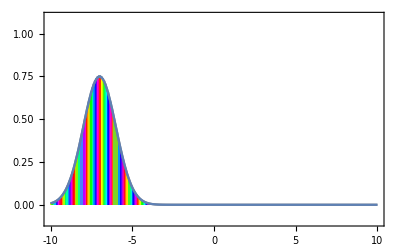

```mathematica
showIt     (* Initial state *)
```

## Animation

```mathematica
dt = 0.005;
```

The time between two of the frames is  20*0.005=0.1:

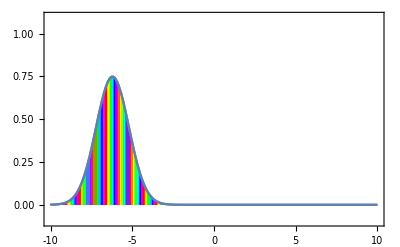
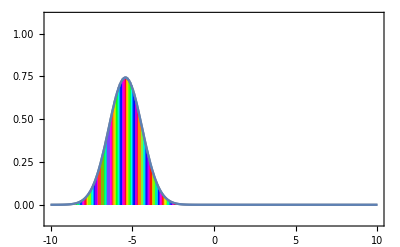
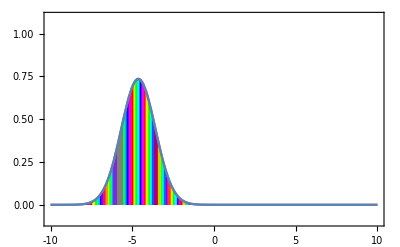
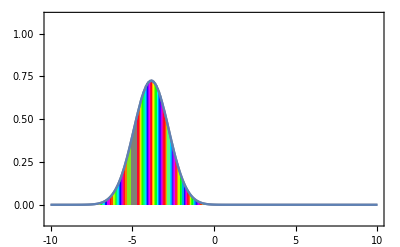
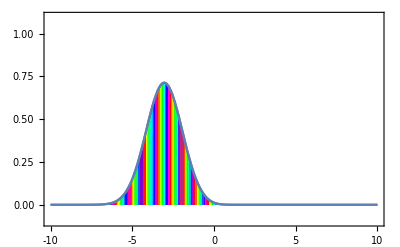
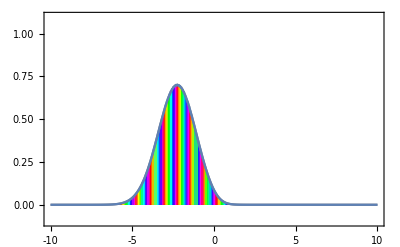
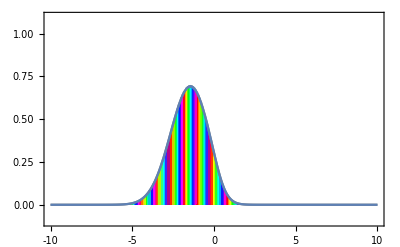
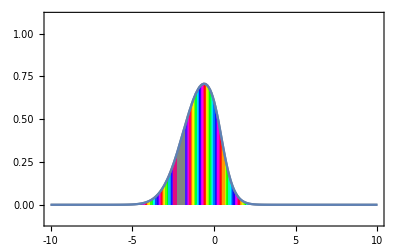

```mathematica
qtab=Table[QTimeEvolution[H,psi,dt,0,20]; showIt, {24}]
```

```mathematica
ListAnimate[qtab]
```

More About

Related Tutorials

QuantumKernel2D